# M1: The Simple Pendulum Matthew Kaiser Summary of experiment: In the experiemnt we used a simple pedulum model to measure the acceleration of gravity, our error in measurement, the dependence of of the length of a pendulum on its period, and used our data to illustrate why a small angle is needed to test for the acceleration of gravity. We determined The acceleration of gravity by measuring the length of the complete system, which includes half of the length of the mass, and measuring the length of the period with the mass starting three degrees from the vertical. Then using our recorded data we were able to compute our value for the acceleration of gravity, and calulated the error and change in g from its true value. Next we measured four other strings lenghts with the added half length of mass m, measuring each length for time to complete a period of motion, and found that a longer length of string coorelated to a longer period. Last we used our string that was closest to one meter in length to test for its period length when starting from various angles to test for a coorelation between greater amplitude and period length, finding that a greater amplitude will cause a longer period for the pendulum. DATA Part 1

```mathematica
LengthOfSM = 1.0864;
PeriodT = 2.0785;
ErrorL= 0.0006;
ErrorT= 0.0008;
g = (4π^2*LengthOfSM )/ (PeriodT^2)
```

9.92772

```mathematica
errorG = g*√(((ErrorL/ LengthOfSM)^2)+((2(ErrorT/PeriodT))^2) )
```

0.00940562

We got a value for g of (9.927±0.009) m/s^2

```mathematica
gKnown = 9.796; (*m/s^2*)
deltag = g - gKnown
```

0.131718

Part 2

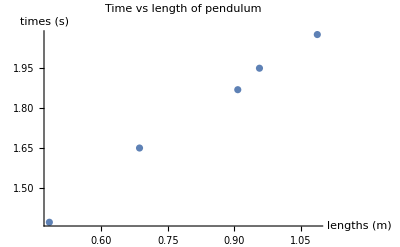

```mathematica
LOM = 0.0264; (*m*)
errorLOM = 0.0001;
lengths = {0.4573+ LOM, 0.6601 + LOM, 0.8811 + LOM, 0.9299 +LOM, 1.0864} (*m*);
times = {1.370, 1.650, 1.870, 1.951, 2.078} (*s*);

 data = Thread[{lengths,times}];
ListPlot [data, AxesLabel-> {"lengths (m)", "times (s)"} , PlotLabel->"Time vs length of pendulum"]
```

The graph of the line repepresenting the time of the period being dependent on the length of the pendulum system, has a hint of a square root graph.

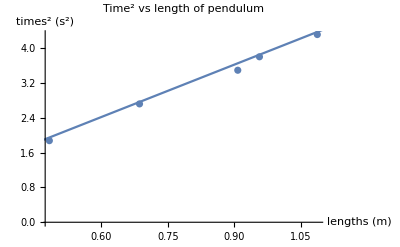

```mathematica
dataN = Thread[{lengths, times^2}];
p1 = ListPlot [dataN, AxesLabel-> {"lengths (m)", "times^2 (s^2)"}, PlotLabel->"Time^2 vs length of pendulum"];
p2= Plot[y[x] = (4 π^2/ gKnown) *x,{x,0,1.2}];
Show [p1, p2]
```

The graph of the time being squared, turns the square root aspect of the graph into being more linear.  Graphing our data points along with the line of T^2=(4π^2/g*L)  shows how close it is to the actual value of g.

Part 3

{π/36,π/18,π/12,π/9,(5 π)/36,π/6,(7 π)/36,(2 π)/9,π/4,(5 π)/18,(11 π)/36,π/3,(13 π)/36,(7 π)/18}

{{π/36,1.9564},{π/18,1.9681},{π/12,1.9746},{π/9,1.9804},{(5 π)/36,1.99},{π/6,2.0039},{(7 π)/36,2.0153},{(2 π)/9,2.0322},{π/4,2.0441},{(5 π)/18,2.064},{(11 π)/36,2.0907},{π/3,2.1166},{(13 π)/36,2.1395},{(7 π)/18,2.1749}}

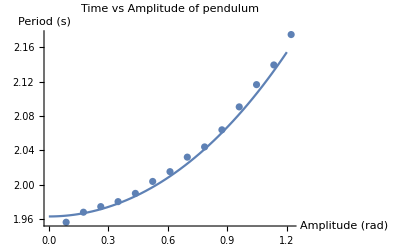

```mathematica
LengthofSMUsed = 0.9563; (*This was the length closest to one meter*)
rad = π/180;
degrees = { 5,10,15,20,25,30,35,40,45,50,55,60,65,70};
radians = (rad*degrees)
periods = { 1.9564, 1.9681, 1.9746, 1.9804, 1.9900, 2.0039, 2.0153, 2.0322, 2.0441, 2.0640, 2.0907,2.1166,2.1395,2.1749};
dataRad = Thread[{radians,periods}]
p3 = ListPlot [dataRad, AxesLabel -> {"Amplitude (rad)","Period (s)"},
PlotLabel -> "Time vs Amplitude of pendulum"];
p4 =Plot [(2π*(√(LengthofSMUsed/gKnown))(1+((1/16)*x^2)+((11/3072)*x^4))), {x, 0, 1.2}];
Show[p3,p4]
```

The graph shows that the increase of amplitude casues a longer period for the pendulum, when compared to the line of 2π*(√(L/gKnown))(1+((1/16)*x^2)+((11/3072)*x^4), the exact solution for the period, we see how precise our measurements are when compared to the exact solution

Discussion of Uncertainty 

 	Systemaic errors could stem from the experiment not being performed in a vaccum, which creates air resisitence, also friction between the string and post create uncertainty. Performing the experiment in a vacuum or using a frictionless pivot would help to reduce our uncertainties.   The air resistence and friction prove to create uncertainties again in part two nd three when measuring period length based on string legth or amplitude of the pendulum’s drop.
 
 Conclusion
 
 	In part one of the experiment we calculated  gravity to equal (9.927 ± 0.009)m/s^2 when compared to the true value of the value gKnown we found an error of (0.131)m/s^2, which is greater than the value we had assumed for the error which told us even though our measurements were precise they could have been more precise.
  	In part two of the experiement we found that  the graph of time vs length looked similar to that of a square root graph. Then grapahed time^2 vs length, and compared our graph to a line of the true solution to the equation, and found that our measured values were accurate to the true value.  We found that the longer the length of the string, the longer the period for the pendulum, which is represented in the graphs in part 2. 
  	In part three of the experiment we used a string-mass system closest to one meter in length.  Our system’s length was (0.9563±0.0002)m,  using the system we measured the period for the system from starting amplitude’s ranging from 5 to 70 increasing by 5 degrees every measurement.  We found that an increase in amplitude leads to an increase in period, and when compared to the true solution for the period we found our dots to be accurate and porecisely in very close proximity to the line of the true solution.